```mathematica
Quit[]
```

```mathematica
rc = 3;
```

```mathematica
wv = 0.5+(rc/v[z])(1-Exp[-v[z]/rc])^2
wx = 0.5+(1/x[z])(1-Exp[-x[z]])^2
f= v[z](1+wv)/(1+z)
g= x[z](1+wx)/(1+z)
```

0.5+(3 (1-ⅇ^(-v[z]/3))^2)/v[z]

0.5+((1-ⅇ^(-x[z]))^2)/x[z]

((1.5+(3 (1-ⅇ^(-v[z]/3))^2)/v[z]) v[z])/(1+z)

((1.5+((1-ⅇ^(-x[z]))^2)/x[z]) x[z])/(1+z)

```mathematica
solv =NDSolve[{v'[z]==f, v[0]==1}, v,{z,0,10}]
```

{{v→InterpolatingFunction[…]}}

```mathematica
solx=NDSolve[{x'[z]==g, x[0]==1/rc}, x,{z,0,10}]
```

{{x→InterpolatingFunction[…]}}

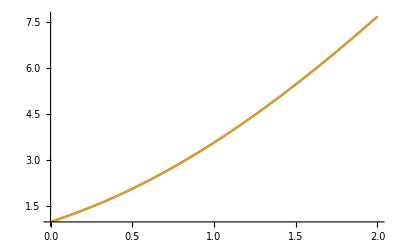

```mathematica
Plot[{Evaluate[x[z]*rc/.solx], Evaluate[v[z]/.solv]},{z,0,2}]
```